I. Function definitions and initial conditions

```mathematica
initialValueOfC=1/2;

s=√(3/4);
nn[T_,m_]:=1/(2 π^2) T^3 (m/T)^2 BesselK[2,m/T] ;

en[T_,m_]:=1/(2 π^2) T^4 (m/T)^2 ((m/T) BesselK[3,m/T] - BesselK[2,m/T]); 
pn[T_,m_]:=T nn[T,m] ;
(* charge density *)
n0[T_,μ_,m_]:=  (2Sinh[μ/T])/π^2 (m/T)^2 T^3 BesselK[2,m/T] ;
n2w[T_,μ_,m_,w2_]:=-w2  (s^2 Sinh[μ/T])/(3 π^2)(m/T)T^3 ( (m/T)BesselK[2,m/T]+2BesselK[3,m/T]) ;
n2k[T_,μ_,m_,k2_]:=-k2  (2 s^2 Sinh[μ/T])/(3 π^2)(m/T)T^3  BesselK[3,m/T] ;
nu[T_,μ_,m_,k2_,w2_]:=n0[T,μ,m]+n2w[T,μ,m,w2]+n2k[T,μ,m,k2];(* energy density *)
e0[T_,μ_,m_]:=(2Cosh[μ/T])/π^2  (m/T)^2 T^4((m/T) BesselK[3,m/T] - BesselK[2,m/T]) ;
e2w[T_,μ_,m_,w2_]:=- w2  (s^2 Cosh[μ/T])/(3 π^2) (m/T)T^4( (m/T)BesselK[2,m/T]+((m/T)^2+10)BesselK[3,m/T]);
e2k[T_,μ_,m_,k2_]:=-k2    (2 s^2 Cosh[μ/T])/(3 π^2) (m/T)T^4( (m/T)BesselK[2,m/T]+5BesselK[3,m/T]);
eu[T_,μ_,m_,k2_,w2_]:=e0[T,μ,m]+e2w[T,μ,m,w2]+e2k[T,μ,m,k2];(* pressure *)
p0[T_,μ_,m_]:=(2Cosh[μ/T])/π^2 (m/T)^2 T^4  BesselK[2,m/T]  ;
p2w[T_,μ_,m_,w2_]:=-w2  (s^2 Cosh[μ/T])/(3 π^2) (m/T)T^4( (m/T)BesselK[2,m/T]+4BesselK[3,m/T]) ;
p2k[T_,μ_,m_,k2_]:=-k2  (4 s^2 Cosh[μ/T])/(3 π^2) (m/T)T^4 BesselK[3,m/T] ;
pΔ[T_,μ_,m_,k2_,w2_]:=p0[T,μ,m]+p2w[T,μ,m,w2]+p2k[T,μ,m,k2]
pkw[T_,μ_,m_]:= -4  Cosh[μ/T] 1/(2 π^2)  s^2/3 T^4 (m/T)( BesselK[3,m/T]) ;
(* spin density *)
a1[T_,μ_,m_]:=(2 s^2 Cosh[μ/T])/(3 π^2) m/T T^3(m/T BesselK[2,m/T]+2 BesselK[3,m/T]) ;
(*a2[T_,μ_,m_]:=(4 s^2 Cosh[μ/T])/(3 π^2)( m/T)^2 T^3 BesselK[4,m/T] ;*)
a3[T_,μ_,m_]:=- (4 s^2 Cosh[μ/T])/(3 π^2)m/T T^3 BesselK[3,m/T] ;
(*a[T_,μ_,m_]:=a1[T,μ,m]-1/2 a2[T,μ,m]-a3[T,μ,m]//FullSimplify*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
j021i=Exp@*Interpolation[MapThread[{{#1,Round[#2,0.1]},#3,{#4,#5}}&,Transpose@ToExpression@Import["j021logv2r.csv"]]];
j022i=Exp@*Interpolation[MapThread[{{#1,Round[#2,0.1]},#3,{#4,#5}}&,Transpose@ToExpression@Import["j022logv2r.csv"]]];
j040i=Exp@*Interpolation[MapThread[{{#1,Round[#2,0.1]},#3,{#4,#5}}&,Transpose@ToExpression@Import["j040logv2r.csv"]]];
j121i=Exp@*Interpolation[MapThread[{{#1,Round[#2,0.1]},#3,{#4,#5}}&,Transpose@ToExpression@Import["j121logv2r.csv"]]];
j123i=Exp@*Interpolation[MapThread[{{#1,Round[#2,0.1]},#3,{#4,#5}}&,Transpose@ToExpression@Import["j123logv2r.csv"]]];
j141i=Exp@*Interpolation[MapThread[{{#1,Round[#2,0.1]},#3,{#4,#5}}&,Transpose@ToExpression@Import["j141logv2r.csv"]]];
j221i=Exp@*Interpolation[MapThread[{{#1,Round[#2,0.1]},#3,{#4,#5}}&,Transpose@ToExpression@Import["j221logv2r.csv"]]];
j222i=Exp@*Interpolation[MapThread[{{#1,Round[#2,0.1]},#3,{#4,#5}}&,Transpose@ToExpression@Import["j222logv2r.csv"]]];
j223i=Exp@*Interpolation[MapThread[{{#1,Round[#2,0.1]},#3,{#4,#5}}&,Transpose@ToExpression@Import["j223logv2r.csv"]]];
j224i=Exp@*Interpolation[MapThread[{{#1,Round[#2,0.1]},#3,{#4,#5}}&,Transpose@ToExpression@Import["j224logv2r.csv"]]];
j240i=Exp@*Interpolation[MapThread[{{#1,Round[#2,0.1]},#3,{#4,#5}}&,Transpose@ToExpression@Import["j240logv2r.csv"]]];
j241i=Exp@*Interpolation[MapThread[{{#1,Round[#2,0.1]},#3,{#4,#5}}&,Transpose@ToExpression@Import["j241logv2r.csv"]]];
j242i=Exp@*Interpolation[MapThread[{{#1,Round[#2,0.1]},#3,{#4,#5}}&,Transpose@ToExpression@Import["j242logv2r.csv"]]];
j260i=Exp@*Interpolation[MapThread[{{#1,Round[#2,0.1]},#3,{#4,#5}}&,Transpose@ToExpression@Import["j260logv2r.csv"]]];
n0f[T_,μ_,m_]:=m^3/Pi^2(j021i[μ/T,m/T]-j021i[-μ/T,m/T]) ;
n2wf[T_,μ_,m_,w2_]:=-w2 (s^2 m^3)/(18Pi^2)(j221i[μ/T,m/T]-j221i[-μ/T,m/T]+2j223i[μ/T,m/T]-2j223i[-μ/T,m/T]);
n2kf[T_,μ_,m_,k2_]:=-k2 (s^2 m^3)/(9Pi^2)(j241i[μ/T,m/T]-j241i[-μ/T,m/T]);

nuf[T_,μ_,m_,k2_,w2_]:=n0f[T,μ,m]+n2kf[T,μ,m,k2]+n2wf[T,μ,m,w2];
e0f[T_,μ_,m_]:=m^4/Pi^2(j022i[μ/T,m/T] +j022i[-μ/T,m/T]);
e2wf[T_,μ_,m_,w2_]:=-w2(s^2 m^4)/(18Pi^2)(j222i[μ/T,m/T] +j222i[-μ/T,m/T] + 2 j224i[μ/T,m/T]+ 2 j224i[-μ/T,m/T]);
e2kf[T_,μ_,m_,k2_]:=-k2(s^2 m^4)/(9 Pi^2)(j242i[μ/T,m/T]+j242i[-μ/T,m/T]);

euf[T_,μ_,m_,k2_,w2_]:=e0f[T,μ,m]+e2kf[T,μ,m,k2]+e2wf[T,μ,m,w2];p0f[T_,μ_,m_]:=m^4/(3Pi^2)(j040i[μ/T,m/T] +j040i[-μ/T,m/T]  ) ;
p2wf[T_,μ_,m_,w2_]:=-w2(s^2 m^4)/(90Pi^2)(j240i[μ/T,m/T]+j240i[-μ/T,m/T]+4j242i[μ/T,m/T]+4j242i[-μ/T,m/T]);
p2kf[T_,μ_,m_,k2_]:=-k2(2s^2 m^4)/(45Pi^2)(j260i[μ/T,m/T]+j260i[-μ/T,m/T]);
pΔf[T_,μ_,m_,k2_,w2_]:=p0f[T,μ,m]+p2kf[T,μ,m,k2]+p2wf[T,μ,m,w2];
pkwf[T_,μ_,m_]:=(-s^2m^4)/(45Pi^2)(j260i[μ/T,m/T]+j260i[-μ/T,m/T] )  ;
a1f[T_,μ_,m_]:=(s^2 m^3)/(9Pi^2)(j121i[μ/T,m/T]+j121i[-μ/T,m/T]+2j123i[μ/T,m/T]+2j123i[-μ/T,m/T]) ;
a2f[T_,μ_,m_]:=(2s^2m^3)/(3Pi^2)(2j123i[μ/T,m/T]+2j123i[-μ/T,m/T]-j121i[μ/T,m/T]-j121i[-μ/T,m/T]) ;
a3f[T_,μ_,m_]:=(-2s^2 m^3)/(9Pi^2)(j141i[μ/T,m/T]+j141i[-μ/T,m/T])  ;
(*af[T_,μ_,m_]:=a1f[T,μ,m]-1/2 a2f[T,μ,m]-a3f[T,μ,m];*)
(* before solving EOMs, all variables are transformed to fermi using the rule: 1 fm/c = 5.0677 1/GeV *)
hbarc=0.1973269631;

(* mass of Lambda particle *)
M=(1.116 (* GeV *))/hbarc;(* fm^-1 *)


τi=1; (* fm *)
τf=10;(* fm *)


Ti=(0.155 (* GeV *))/hbarc; (* fm^-1 *)

μi=(0.800 (* GeV *))/hbarc; (* fm^-1 *) 


Ckzi=initialValueOfC;
Cwzi=initialValueOfC;
Ckxi=initialValueOfC;
Ckyi=initialValueOfC;
Cwxi=initialValueOfC;
Cwyi=initialValueOfC;
```

II. Solving EOM (1. Longitudinal polarization)

```mathematica
(*eqsNoSpin={
τ D[nu[T[τ],μ[τ],M,0,0],τ]+nu[T[τ],μ[τ],M,0,0]==0,
τ D[eu[T[τ],μ[τ],M,0,0],τ]+eu[T[τ],μ[τ],M,0,0]+pΔ[T[τ],μ[τ],M,0,0]==0
};*)
eqsBoltzmannNoFeedback={
τ D[nu[T[τ],μ[τ],M,0,0],τ]+nu[T[τ],μ[τ],M,0,0]==0,
τ D[eu[T[τ],μ[τ],M,0,0],τ]+eu[T[τ],μ[τ],M,0,0]+pΔ[T[τ],μ[τ],M,0,0]==0,a3[T[τ],μ[τ],M] D[Ckz[τ],τ]+(D[a3[T[τ],μ[τ],M],τ]+a3[T[τ],μ[τ],M]/τ)Ckz[τ]==0,
a1[T[τ],μ[τ],M]D[Cwz[τ],τ]+(D[a1[T[τ],μ[τ],M],τ]+a1[T[τ],μ[τ],M]/τ)Cwz[τ]==0
};
eqsBoltzmannSpinFeedback={
τ D[nu[T[τ],μ[τ],M,-Ckz[τ]^2,-Cwz[τ]^2],τ]+nu[T[τ],μ[τ],M,-Ckz[τ]^2,-Cwz[τ]^2]==0,
τ D[eu[T[τ],μ[τ],M,-Ckz[τ]^2,-Cwz[τ]^2],τ]+(eu[T[τ],μ[τ],M,-Ckz[τ]^2,-Cwz[τ]^2]+pΔ[T[τ],μ[τ],M,-Ckz[τ]^2,-Cwz[τ]^2])
+pkw[T[τ],μ[τ],M](Ckz[τ]^2+Cwz[τ]^2)==0,
a3[T[τ],μ[τ],M]D[Ckz[τ],τ]+(D[a3[T[τ],μ[τ],M],τ]+a3[T[τ],μ[τ],M]/τ)Ckz[τ]==0,
a1[T[τ],μ[τ],M]D[Cwz[τ],τ]+(D[a1[T[τ],μ[τ],M],τ]+a1[T[τ],μ[τ],M]/τ)Cwz[τ]==0
};
```

```mathematica
(* Boltzmann Bjorken solution for T and μ without contributions from spin (line of reference) *)
```

```mathematica
(*solveBoltzmannNoSpin[tinit_,tfin_]:=NDSolve[Flatten[{eqsBoltzmannNoSpin,T[tinit]==Ti,μ[tinit]==μi
}],{T,μ},{τ,tinit,tfin}, Method->Automatic][[1]];
solutionBoltzmannNoSpin=solveBoltzmannNoSpin[1,10];
TsolutionBoltzmannNoSpin=solutionBoltzmannNoSpin[[1,2]];
μsolutionBoltzmannNoSpin=solutionBoltzmannNoSpin[[2,2]];  *)
 (*Boltzmann Bjorken solution with 1st order expansion in Subscript[ω, μν] *)
solveBoltzmannNoFeedback[tinit_,tfin_]:=NDSolve[Flatten[{
eqsBoltzmannNoFeedback,
T[tinit]==Ti,
μ[tinit]==μi,
Ckz[tinit]==Ckzi,
Cwz[tinit]==Cwzi
}],{T,μ,Ckz,Cwz},{τ,tinit,tfin}, Method->"EquationSimplification"->{"Solve", "TimeConstraint"->100}(*{"EquationSimplification"->"Residual"}*)][[1]];
solutionBoltzmannNoFeedback=solveBoltzmannNoFeedback[1,10];
TsolutionBoltzmannNoFeedback=solutionBoltzmannNoFeedback[[1,2]];
μsolutionBoltzmannNoFeedback=solutionBoltzmannNoFeedback[[2,2]] ;
CkzsolutionBoltzmannNoFeedback=solutionBoltzmannNoFeedback[[3,2]];
CwzsolutionBoltzmannNoFeedback=solutionBoltzmannNoFeedback[[4,2]];
(* Boltzmann Bjorken solution for CkZ and CwZ as well as T and μ with 2nd order contributions from spin *)
solveBoltzmannSpinFeedback[tinit_,tfin_]:=NDSolve[Flatten[{
eqsBoltzmannSpinFeedback,
T[tinit]==Ti,
μ[tinit]==μi,
Ckz[tinit]==Ckzi,
Cwz[tinit]==Cwzi
}],{T,μ,Ckz,Cwz},{τ,tinit,tfin}, Method->"EquationSimplification"->{"Solve", "TimeConstraint"->100}(*{"EquationSimplification"->"Residual"}*)][[1]];
solutionBoltzmannSpinFeedback=solveBoltzmannSpinFeedback[1,10];
TsolutionBoltzmannSpinFeedback=solutionBoltzmannSpinFeedback[[1,2]];
μsolutionBoltzmannSpinFeedback=solutionBoltzmannSpinFeedback[[2,2]]; 
CkzsolutionBoltzmannSpinFeedback=solutionBoltzmannSpinFeedback[[3,2]]; 
CwzsolutionBoltzmannSpinFeedback=solutionBoltzmannSpinFeedback[[4,2]];
```

```mathematica
(*eqsFermiNoSpin={
τ D[nuf[T[τ],μ[τ],M,0,0],τ]+nuf[T[τ],μ[τ],M,0,0]==0,
τ D[euf[T[τ],μ[τ],M,0,0],τ]+euf[T[τ],μ[τ],M,0,0]+pΔf[T[τ],μ[τ],M,0,0]==0
};*)
eqsFermiNoFeedback={
τ D[nuf[T[τ],μ[τ],M,0,0],τ]+nuf[T[τ],μ[τ],M,0,0]==0,
τ D[euf[T[τ],μ[τ],M,0,0],τ]+euf[T[τ],μ[τ],M,0,0]+pΔf[T[τ],μ[τ],M,0,0]==0,a3f[T[τ],μ[τ],M] D[Ckz[τ],τ]+(D[a3f[T[τ],μ[τ],M],τ]+a3f[T[τ],μ[τ],M]/τ)Ckz[τ]==0,
a1f[T[τ],μ[τ],M]D[Cwz[τ],τ]+(D[a1f[T[τ],μ[τ],M],τ]+a1f[T[τ],μ[τ],M]/τ)Cwz[τ]==0
};
eqsFermiSpinFeedback={
τ D[nuf[T[τ],μ[τ],M,-Ckz[τ]^2,-Cwz[τ]^2],τ]+nuf[T[τ],μ[τ],M,-Ckz[τ]^2,-Cwz[τ]^2]==0,
τ D[euf[T[τ],μ[τ],M,-Ckz[τ]^2,-Cwz[τ]^2],τ]+euf[T[τ],μ[τ],M,-Ckz[τ]^2,-Cwz[τ]^2]+pΔf[T[τ],μ[τ],M,-Ckz[τ]^2,-Cwz[τ]^2]+pkwf[T[τ],μ[τ],M](Ckz[τ]^2+Cwz[τ]^2)==0,
a3f[T[τ],μ[τ],M]D[Ckz[τ],τ]+(D[a3f[T[τ],μ[τ],M],τ]+a3f[T[τ],μ[τ],M]/τ)Ckz[τ]==0,
a1f[T[τ],μ[τ],M]D[Cwz[τ],τ]+(D[a1f[T[τ],μ[τ],M],τ]+a1f[T[τ],μ[τ],M]/τ)Cwz[τ]==0
};
```

```mathematica
(*solveFermiNoSpin[tinit_,tfin_]:=NDSolve[Flatten[{
eqsFermiNoSpin,
T[tinit]==Ti,
μ[tinit]==μi
}],{T,μ},{τ,tinit,tfin}, Method->"EquationSimplification"->{"Solve", "TimeConstraint"->100}(*{"EquationSimplification"->"Residual"}*)][[1]];
solutionFermiNoSpin=solveFermiNoSpin[1,10];
TsolutionFermiNoSpin=solutionFermiNoSpin[[1,2]];
μsolutionFermiNoSpin=solutionFermiNoSpin[[2,2]];  *)
(* Fermi-Dirac Bjorken solution with 1st order expansion in Subscript[ω, μν]*)
solveFermiNoFeedback[tinit_,tfin_]:=NDSolve[Flatten[{
eqsFermiNoFeedback,
T[tinit]==Ti,
μ[tinit]==μi,
Ckz[tinit]==Ckzi,
Cwz[tinit]==Cwzi
}],{T,μ,Ckz,Cwz},{τ,tinit,tfin},Method->"EquationSimplification"->{"Solve", "TimeConstraint"->100}(*{"EquationSimplification"->"Residual"}*),MaxStepSize->0.001,MaxSteps->10000][[1]];
solutionFermiNoFeedback=solveFermiNoFeedback[1,10];
TsolutionFermiNoFeedback=solutionFermiNoFeedback[[1,2]];
μsolutionFermiNoFeedback=solutionFermiNoFeedback[[2,2]] ;
CkzsolutionFermiNoFeedback=solutionFermiNoFeedback[[3,2]];
CwzsolutionFermiNoFeedback=solutionFermiNoFeedback[[4,2]];
(* Fermi-Dirac Bjorken solution for CkZ and CwZ as well as T and μ with 2nd order contributions from spin *)
solveFermiSpinFeedback[τinit_,τfin_]:=NDSolve[Flatten[{
eqsFermiSpinFeedback,
T[τi]==Ti,
μ[τi]==μi,
Ckz[τi]==Ckzi,
Cwz[τi]==Cwzi
}],{T,μ,Ckz,Cwz},{τ,τinit,τfin},Method->"EquationSimplification"->{"Solve", "TimeConstraint"->100}(*{"EquationSimplification"->"Residual"}*),MaxStepSize->0.001,MaxSteps->10000][[1]];

solutionFermiSpinFeedback=solveFermiSpinFeedback[1,10];
TsolutionFermiSpinFeedback=solutionFermiSpinFeedback[[1,2]];
μsolutionFermiSpinFeedback=solutionFermiSpinFeedback[[2,2]]; 
CkzsolutionFermiSpinFeedback=solutionFermiSpinFeedback[[3,2]]; 
CwzsolutionFermiSpinFeedback=solutionFermiSpinFeedback[[4,2]];
```

IV . Plot Solutions (1. Longitudinal polarization)

### PRC 2e

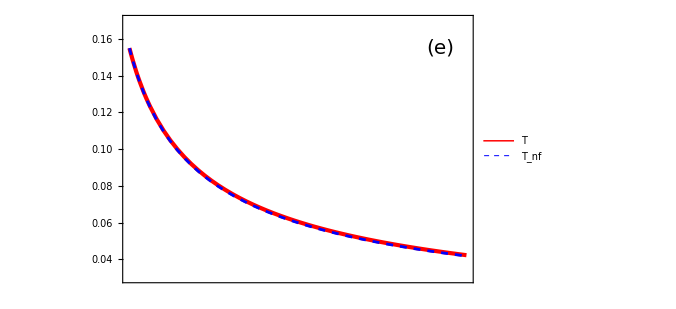

```mathematica
Plot[{TsolutionBoltzmannSpinFeedback[τ]hbarc,TsolutionBoltzmannNoFeedback[τ]hbarc},{τ,1.0,10.0},PlotRange->{{1,10},{0.03,0.17}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},
Axes->False,ImageSize->500,Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{{{0.04,"0.04",0.03},{0.035,"",0.01},{0.045,"",0.01},{0.05,"",0.015},{0.055,"",0.01},{0.06,"0.06",0.03},{0.065,"",0.01},{0.07,"",0.015},{0.075,"",0.01},{0.08,"0.08",0.03},{0.085,"",0.01},{0.09,"",0.015},{0.095,"",0.01},{0.10,"0.10",0.03},{0.105,"",0.01},{0.11,"",0.015},{0.115,"",0.01},{0.12,"0.12",0.03},{0.125,"",0.01},{0.13,"",0.015},{0.135,"",0.01},{0.14,"0.14",0.03},{0.145,"",0.01},{0.15,"",0.015},{0.155,"",0.01},{0.16,"0.16",0.03},{0.165,"",0.01}},None},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},None}},
Epilog->{Text[Style["(e)",FontSize->20],{9.3,0.155}],Rotate[Text[Style["T [GeV]",FontSize->19],{-0.3,0.1}],90Degree]},
PlotLegends->Placed[LineLegend[{"T","T_nf"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.85,0.35}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,10}}]
```

### PRC2f

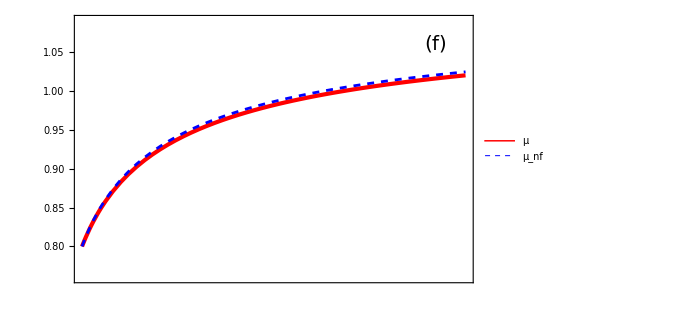

```mathematica
Plot[{μsolutionBoltzmannSpinFeedback[τ]hbarc,μsolutionBoltzmannNoFeedback[τ]hbarc},{τ,1.0,10.0},PlotRange->{{1,10},{0.76,1.09}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},Axes->False,ImageSize->500,
Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{None,{{0.77,"",0.015},{0.78,"",0.015},{0.79,"",0.015},{0.80,"0.80",0.03},{0.81,"",0.015},{0.82,"",0.015},{0.83,"",0.015},{0.84,"",0.015},{0.85,"0.85",0.03},{0.86,"",0.015},{0.87,"",0.015},{0.88,"",0.015},{0.89,"",0.015},{0.9,"0.90",0.03},{0.91,"",0.015},{0.92,"",0.015},{0.93,"",0.015},{0.94,"",0.015},{0.95,"0.95",0.03},{0.96,"",0.015},{0.97,"",0.015},{0.98,"",0.015},{0.99,"",0.015},{1,"1.00",0.03},{1.01,"",0.015},{1.02,"",0.015},{1.03,"",0.015},{1.04,"",0.015},{1.05,"1.05",0.03},{1.06,"",0.015},{1.07,"",0.015},{1.08,"",0.015},{1.10,"1.10",0.03}}},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},None}},
Epilog->{Text[Style["(f)",FontSize->20],{9.3,1.06}],Rotate[Text[Style["μ [GeV]",FontSize->19],{11.4,0.94}],-90Degree]},
PlotLegends->Placed[LineLegend[{"μ","μ_nf"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.35,0.8}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,10}}]
```

### PRC2g

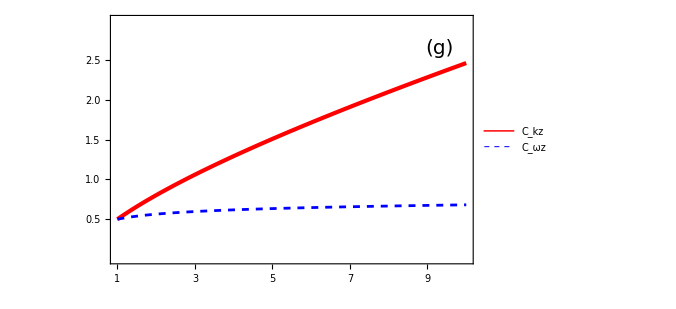

```mathematica
Plot[{CkzsolutionBoltzmannSpinFeedback[τ],CwzsolutionBoltzmannSpinFeedback[τ]} ,{τ,1.0,10.0},PlotRange->{{1,10},{0,3.0}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},Axes->False,ImageSize->500,
Frame->True,FrameStyle->Directive[Black, Thickness[0.008],14],

FrameTicks->{{{{0.25,"", 0.015},{0.5,"0.5",0.03},{0.75,"",0.015},{1.,"1.0",0.03},{1.25,"",0.015},{1.5,"1.5", 0.03},{1.75,"",0.015},{2.,"2.0",0.03},{2.25,"",0.015},{2.5,"2.5", 0.03},{2.75,"",0.015}},None},
{{1,{1.5,"",0.015},{2.,"2",0.03},{2.5,"",0.015},{3.,"3",0.03},{3.5,"",0.015},{4.,"4",0.03},{4.5,"",0.015},{5.,"5",0.03},{5.5,"",0.015},{6.,"6",0.03},{6.5,"",0.015},{7.,"7",0.03},{7.5,"",0.015},{8.,"8",0.03},{8.5,"",0.015},{9.,"9",0.03},{9.5,"",0.015},{9.8,"10",0}},{1,{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015},10}}},
Epilog->{Text[Style["(g)",FontSize->20],{9.3,2.65}],Text[Style["τ [fm]",FontSize->19],{5.5,-0.45}],Rotate[Text[Style["C_k, C_ω",FontSize->19],{-0.1,1.5}],90Degree]},
PlotLegends->Placed[LineLegend[{"C_kz","C_ωz"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.2,0.75}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,5}}]
```

### PRC2h

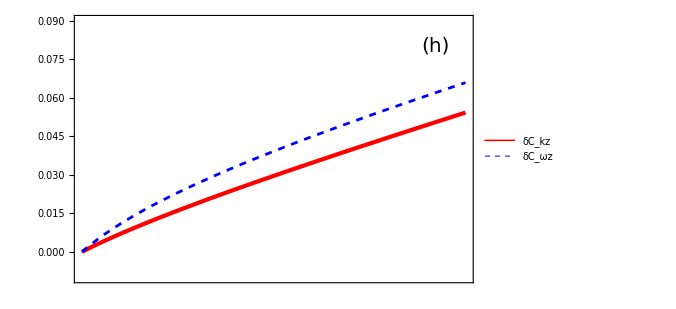

```mathematica
Plot[{CkzsolutionBoltzmannSpinFeedback[τ]/CkzsolutionBoltzmannNoFeedback[τ]-1,CwzsolutionBoltzmannSpinFeedback[τ]/CwzsolutionBoltzmannNoFeedback[τ]-1},{τ,1.0,10.0},PlotRange->{{1,10},{-0.01,0.09}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},Axes->False,ImageSize->500,
Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{None,{{0.0,"0",0.03},{0.01,"",0.015},{0.02,"0.02",0.03},{0.03,"",0.015},{0.04,"0.04",0.03},{0.05,"",0.015},{0.06,"0.06",0.03},{0.07,"",0.015},{0.08,"0.08",0.03}}},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},None}},
Epilog->{Text[Style["(h)",FontSize->20],{9.3,0.08}],Rotate[Text[Style["δC_k,δC_w",FontSize->19],{11.4,0.04}],-90Degree]},
PlotLegends->Placed[LineLegend[{"δC_kz","δC_ωz"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.2,0.8}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,10}}]
```

### Fermi 2e

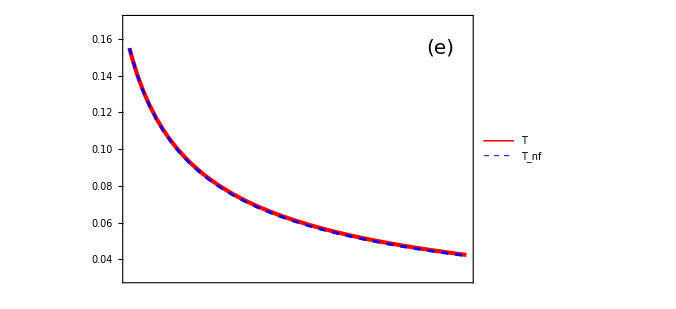

```mathematica
Plot[{TsolutionFermiSpinFeedback[τ]hbarc,TsolutionFermiNoFeedback[τ]hbarc},{τ,1.0,10.0},PlotRange->{{1,10},{0.03,0.17}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},
Axes->False,ImageSize->500,Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{{{0.04,"0.04",0.03},{0.035,"",0.01},{0.045,"",0.01},{0.05,"",0.015},{0.055,"",0.01},{0.06,"0.06",0.03},{0.065,"",0.01},{0.07,"",0.015},{0.075,"",0.01},{0.08,"0.08",0.03},{0.085,"",0.01},{0.09,"",0.015},{0.095,"",0.01},{0.10,"0.10",0.03},{0.105,"",0.01},{0.11,"",0.015},{0.115,"",0.01},{0.12,"0.12",0.03},{0.125,"",0.01},{0.13,"",0.015},{0.135,"",0.01},{0.14,"0.14",0.03},{0.145,"",0.01},{0.15,"",0.015},{0.155,"",0.01},{0.16,"0.16",0.03},{0.165,"",0.01}},None},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},None}},
Epilog->{Text[Style["(e)",FontSize->20],{9.3,0.155}],Rotate[Text[Style["T [GeV]",FontSize->19],{-0.3,0.1}],90Degree]},
PlotLegends->Placed[LineLegend[{"T","T_nf"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.85,0.35}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,10}}]
```

### Fermi 2f

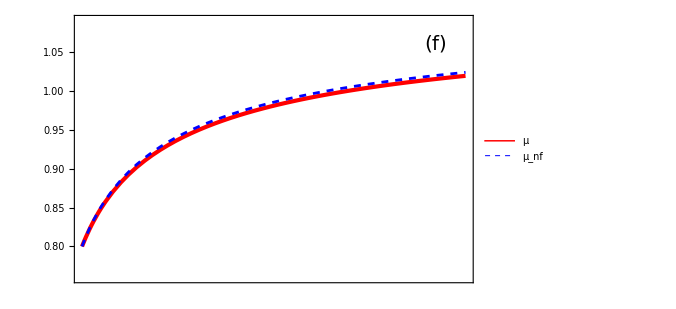

```mathematica
Plot[{μsolutionFermiSpinFeedback[τ]hbarc,μsolutionFermiNoFeedback[τ]hbarc},{τ,1.0,10.0},PlotRange->{{1,10},{0.76,1.09}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},Axes->False,ImageSize->500,
Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{None,{{0.77,"",0.015},{0.78,"",0.015},{0.79,"",0.015},{0.80,"0.80",0.03},{0.81,"",0.015},{0.82,"",0.015},{0.83,"",0.015},{0.84,"",0.015},{0.85,"0.85",0.03},{0.86,"",0.015},{0.87,"",0.015},{0.88,"",0.015},{0.89,"",0.015},{0.9,"0.90",0.03},{0.91,"",0.015},{0.92,"",0.015},{0.93,"",0.015},{0.94,"",0.015},{0.95,"0.95",0.03},{0.96,"",0.015},{0.97,"",0.015},{0.98,"",0.015},{0.99,"",0.015},{1,"1.00",0.03},{1.01,"",0.015},{1.02,"",0.015},{1.03,"",0.015},{1.04,"",0.015},{1.05,"1.05",0.03},{1.06,"",0.015},{1.07,"",0.015},{1.08,"",0.015},{1.10,"1.10",0.03}}},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},None}},
Epilog->{Text[Style["(f)",FontSize->20],{9.3,1.06}],Rotate[Text[Style["μ [GeV]",FontSize->19],{11.4,0.94}],-90Degree]},
PlotLegends->Placed[LineLegend[{"μ","μ_nf"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.35,0.8}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,10}}]
```

### Fermi2g

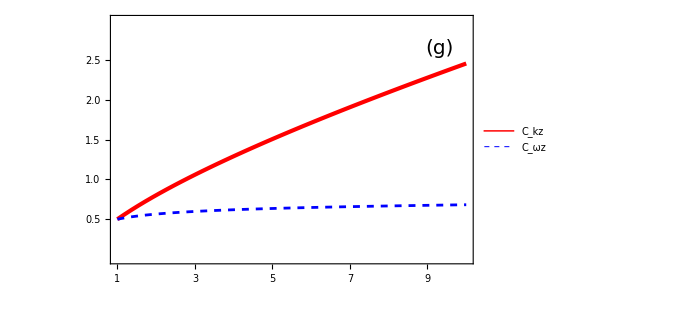

```mathematica
Plot[{CkzsolutionFermiSpinFeedback[τ],CwzsolutionFermiSpinFeedback[τ]} ,{τ,1.0,10.0},PlotRange->{{1,10},{0,3.0}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},Axes->False,ImageSize->500,
Frame->True,FrameStyle->Directive[Black, Thickness[0.008],14],

FrameTicks->{{{{0.25,"", 0.015},{0.5,"0.5",0.03},{0.75,"",0.015},{1.,"1.0",0.03},{1.25,"",0.015},{1.5,"1.5", 0.03},{1.75,"",0.015},{2.,"2.0",0.03},{2.25,"",0.015},{2.5,"2.5", 0.03},{2.75,"",0.015}},None},
{{1,{1.5,"",0.015},{2.,"2",0.03},{2.5,"",0.015},{3.,"3",0.03},{3.5,"",0.015},{4.,"4",0.03},{4.5,"",0.015},{5.,"5",0.03},{5.5,"",0.015},{6.,"6",0.03},{6.5,"",0.015},{7.,"7",0.03},{7.5,"",0.015},{8.,"8",0.03},{8.5,"",0.015},{9.,"9",0.03},{9.5,"",0.015},{9.8,"10",0}},{1,{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015},10}}},
Epilog->{Text[Style["(g)",FontSize->20],{9.3,2.65}],Text[Style["τ [fm]",FontSize->19],{5.5,-0.45}],Rotate[Text[Style["C_k, C_ω",FontSize->19],{-0.1,1.5}],90Degree]},
PlotLegends->Placed[LineLegend[{"C_kz","C_ωz"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.2,0.75}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,5}}]
```

### Fermi 2h

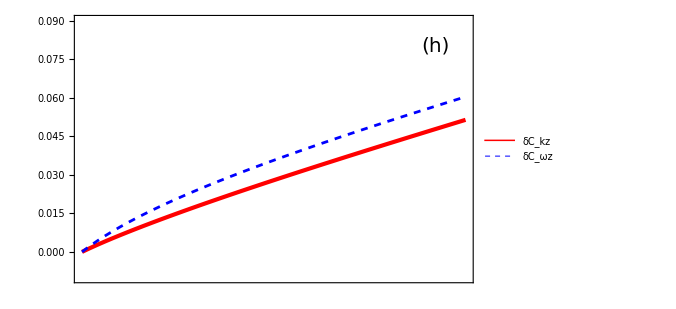

```mathematica
Plot[{CkzsolutionFermiSpinFeedback[τ]/CkzsolutionFermiNoFeedback[τ]-1,CwzsolutionFermiSpinFeedback[τ]/CwzsolutionFermiNoFeedback[τ]-1},{τ,1.0,10.0},PlotRange->{{1,10},{-0.01,0.09}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},Axes->False,ImageSize->500,
Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{None,{{0.0,"0",0.03},{0.01,"",0.015},{0.02,"0.02",0.03},{0.03,"",0.015},{0.04,"0.04",0.03},{0.05,"",0.015},{0.06,"0.06",0.03},{0.07,"",0.015},{0.08,"0.08",0.03}}},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},None}},
Epilog->{Text[Style["(h)",FontSize->20],{9.3,0.08}],Rotate[Text[Style["δC_k,δC_w",FontSize->19],{11.4,0.04}],-90Degree]},
PlotLegends->Placed[LineLegend[{"δC_kz","δC_ωz"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.2,0.8}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,10}}]
```

### Fermi 2n

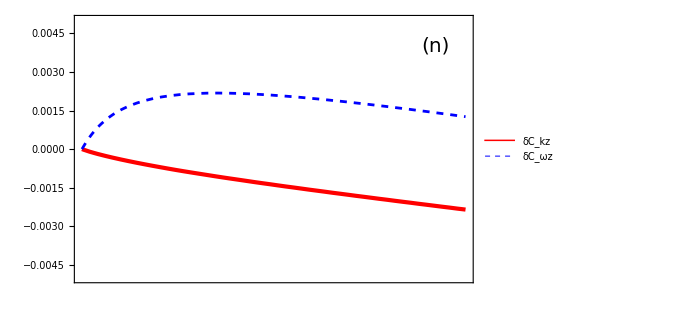

```mathematica
Plot[{CkzsolutionFermiSpinFeedback[τ]/CkzsolutionBoltzmannSpinFeedback[τ]-1,CwzsolutionFermiSpinFeedback[τ]/CwzsolutionBoltzmannSpinFeedback[τ]-1},{τ,1.0,10.0},PlotRange->{{1,10},{-0.005,0.005}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},Axes->False,ImageSize->500,
Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{None,{{-0.004,"-0.004",0.03},{-0.003,"",0.015},{-0.002,"-0.002",0.03},{-0.001,"",0.015},{0,"0",0.03},{0.001,"",0.015},{0.002,"0.002",0.03},{0.003,"",0.015},{0.004,"0.004",0.03}}},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},None}},
Epilog->{Text[Style["(n)",FontSize->20],{9.3,0.004}],Rotate[Text[Style["δC_k,δC_w",FontSize->19],{11.4,0.0005}],-90Degree]},
PlotLegends->Placed[LineLegend[{"δC_kz","δC_ωz"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.25,0.2}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,10}}]
```

V. Solving EOM (2. Transverse polarization)

```mathematica
eqsBoltzmannNoFeedbackTransverse={
τ D[nu[T[τ],μ[τ],M,0,0],τ]+nu[T[τ],μ[τ],M,0,0]==0,
τ D[eu[T[τ],μ[τ],M,0,0],τ]+eu[T[τ],μ[τ],M,0,0]+pΔ[T[τ],μ[τ],M,0,0]==0,
a3[T[τ],μ[τ],M]D[Ckx[τ],τ]+(D[a3[T[τ],μ[τ],M],τ]+(3/2 a3[T[τ],μ[τ],M])/τ)Ckx[τ]==0,
a3[T[τ],μ[τ],M]D[Cky[τ],τ]+(D[a3[T[τ],μ[τ],M],τ]+(3/2 a3[T[τ],μ[τ],M])/τ)Cky[τ]==0,
a1[T[τ],μ[τ],M]D[Cwx[τ],τ]+(D[a1[T[τ],μ[τ],M],τ]+(a1[T[τ],μ[τ],M]-1/2 a3[T[τ],μ[τ],M])/τ)Cwx[τ]==0,
a1[T[τ],μ[τ],M]D[Cwy[τ],τ]+(D[a1[T[τ],μ[τ],M],τ]+(a1[T[τ],μ[τ],M]-1/2 a3[T[τ],μ[τ],M])/τ)Cwy[τ]==0
};
eqsBoltzmannSpinFeedbackTransverse={
τ D[nu[T[τ],μ[τ],M,-Ckx[τ]^2-Cky[τ]^2,-Cwx[τ]^2-Cwy[τ]^2],τ]+nu[T[τ],μ[τ],M,-Ckx[τ]^2-Cky[τ]^2,-Cwx[τ]^2-Cwy[τ]^2]==0,
τ D[eu[T[τ],μ[τ],M,-Ckx[τ]^2-Cky[τ]^2,-Cwx[τ]^2-Cwy[τ]^2],τ]+eu[T[τ],μ[τ],M,-Ckx[τ]^2-Cky[τ]^2,-Cwx[τ]^2-Cwy[τ]^2]+pΔ[T[τ],μ[τ],M,-Ckx[τ]^2-Cky[τ]^2,-Cwx[τ]^2-Cwy[τ]^2]==0,
a3[T[τ],μ[τ],M]D[Ckx[τ],τ]+(D[a3[T[τ],μ[τ],M],τ]+(3/2 a3[T[τ],μ[τ],M])/τ)Ckx[τ]==0,
a3[T[τ],μ[τ],M]D[Cky[τ],τ]+(D[a3[T[τ],μ[τ],M],τ]+(3/2 a3[T[τ],μ[τ],M])/τ)Cky[τ]==0,
a1[T[τ],μ[τ],M]D[Cwx[τ],τ]+(D[a1[T[τ],μ[τ],M],τ]+(a1[T[τ],μ[τ],M]-1/2 a3[T[τ],μ[τ],M])/τ)Cwx[τ]==0,
a1[T[τ],μ[τ],M]D[Cwy[τ],τ]+(D[a1[T[τ],μ[τ],M],τ]+(a1[T[τ],μ[τ],M]-1/2 a3[T[τ],μ[τ],M])/τ)Cwy[τ]==0
};
eqsFermiNoFeedbackTransverse={
τ D[nuf[T[τ],μ[τ],M,0,0],τ]+nuf[T[τ],μ[τ],M,0,0]==0,
τ D[euf[T[τ],μ[τ],M,0,0],τ]+euf[T[τ],μ[τ],M,0,0]+pΔf[T[τ],μ[τ],M,0,0]==0,
a3f[T[τ],μ[τ],M]D[Ckx[τ],τ]+(D[a3f[T[τ],μ[τ],M],τ]+(3/2 a3f[T[τ],μ[τ],M])/τ)Ckx[τ]==0,
a3f[T[τ],μ[τ],M]D[Cky[τ],τ]+(D[a3f[T[τ],μ[τ],M],τ]+(3/2 a3f[T[τ],μ[τ],M])/τ)Cky[τ]==0,
a1f[T[τ],μ[τ],M]D[Cwx[τ],τ]+(D[a1f[T[τ],μ[τ],M],τ]+(a1f[T[τ],μ[τ],M]-1/2 a3f[T[τ],μ[τ],M])/τ)Cwx[τ]==0,
a1f[T[τ],μ[τ],M]D[Cwy[τ],τ]+(D[a1f[T[τ],μ[τ],M],τ]+(a1f[T[τ],μ[τ],M]-1/2 a3f[T[τ],μ[τ],M])/τ)Cwy[τ]==0
};
eqsFermiSpinFeedbackTransverse={
τ D[nuf[T[τ],μ[τ],M,-Ckx[τ]^2-Cky[τ]^2,-Cwx[τ]^2-Cwy[τ]^2],τ]+nuf[T[τ],μ[τ],M,-Ckx[τ]^2-Cky[τ]^2,-Cwx[τ]^2-Cwy[τ]^2]==0,
τ D[euf[T[τ],μ[τ],M,-Ckx[τ]^2-Cky[τ]^2,-Cwx[τ]^2-Cwy[τ]^2],τ]+euf[T[τ],μ[τ],M,-Ckx[τ]^2-Cky[τ]^2,-Cwx[τ]^2-Cwy[τ]^2]+pΔf[T[τ],μ[τ],M,-Ckx[τ]^2-Cky[τ]^2,-Cwx[τ]^2-Cwy[τ]^2]==0,
a3f[T[τ],μ[τ],M]D[Ckx[τ],τ]+(D[a3f[T[τ],μ[τ],M],τ]+(3/2 a3f[T[τ],μ[τ],M])/τ)Ckx[τ]==0,
a3f[T[τ],μ[τ],M]D[Cky[τ],τ]+(D[a3f[T[τ],μ[τ],M],τ]+(3/2 a3f[T[τ],μ[τ],M])/τ)Cky[τ]==0,
a1f[T[τ],μ[τ],M]D[Cwx[τ],τ]+(D[a1f[T[τ],μ[τ],M],τ]+(a1f[T[τ],μ[τ],M]-1/2 a3f[T[τ],μ[τ],M])/τ)Cwx[τ]==0,
a1f[T[τ],μ[τ],M]D[Cwy[τ],τ]+(D[a1f[T[τ],μ[τ],M],τ]+(a1f[T[τ],μ[τ],M]-1/2 a3f[T[τ],μ[τ],M])/τ)Cwy[τ]==0
};
```

```mathematica
solveBoltzmannNoFeedbackTransverse[tinit_,tfin_]:=NDSolve[Flatten[{
eqsBoltzmannNoFeedbackTransverse,
T[tinit]==Ti,
μ[tinit]==μi,
Ckx[tinit]==Ckxi,
Cky[tinit]==Ckyi,
Cwx[tinit]==Cwxi,
Cwy[tinit]==Cwyi
}],{T,μ,Ckx,Cky,Cwx,Cwy},{τ,tinit,tfin}, Method->"EquationSimplification"->{"Solve", "TimeConstraint"->100}(*{"EquationSimplification"->"Residual"}*)][[1]];

solutionBoltzmannNoFeedbackTransverse=solveBoltzmannNoFeedbackTransverse[1,10];
TsolutionBoltzmannNoFeedbackTransverse=solutionBoltzmannNoFeedbackTransverse[[1,2]];
μsolutionBoltzmannNoFeedbackTransverse=solutionBoltzmannNoFeedbackTransverse[[2,2]] ;
CkxsolutionBoltzmannNoFeedbackTransverse=solutionBoltzmannNoFeedbackTransverse[[3,2]];
CkysolutionBoltzmannNoFeedbackTransverse=solutionBoltzmannNoFeedbackTransverse[[4,2]];
CwxsolutionBoltzmannNoFeedbackTransverse=solutionBoltzmannNoFeedbackTransverse[[5,2]];
CwysolutionBoltzmannNoFeedbackTransverse=solutionBoltzmannNoFeedbackTransverse[[6,2]];

solveBoltzmannSpinFeedbackTransverse[tinit_,tfin_]:=NDSolve[Flatten[{
eqsBoltzmannSpinFeedbackTransverse,
T[tinit]==Ti,
μ[tinit]==μi,
Ckx[tinit]==Ckxi,
Cky[tinit]==Ckyi,
Cwx[tinit]==Cwxi,
Cwy[tinit]==Cwyi
}],{T,μ,Ckx,Cky,Cwx,Cwy},{τ,tinit,tfin}, Method->"EquationSimplification"->{"Solve", "TimeConstraint"->100}(*{"EquationSimplification"->"Residual"}*)][[1]];

solutionBoltzmannSpinFeedbackTransverse=solveBoltzmannSpinFeedbackTransverse[1,10];
TsolutionBoltzmannSpinFeedbackTransverse=solutionBoltzmannSpinFeedbackTransverse[[1,2]];
μsolutionBoltzmannSpinFeedbackTransverse=solutionBoltzmannSpinFeedbackTransverse[[2,2]] ;
CkxsolutionBoltzmannSpinFeedbackTransverse=solutionBoltzmannSpinFeedbackTransverse[[3,2]];
CkysolutionBoltzmannSpinFeedbackTransverse=solutionBoltzmannSpinFeedbackTransverse[[4,2]];
CwxsolutionBoltzmannSpinFeedbackTransverse=solutionBoltzmannSpinFeedbackTransverse[[5,2]];
CwysolutionBoltzmannSpinFeedbackTransverse=solutionBoltzmannSpinFeedbackTransverse[[6,2]];
```

```mathematica
(* TSolutionFullf - transverse solution for  - 2nd order in Subscript[ω, μν] calculations *)
```

```mathematica
solveFermiNoFeedbackTransverse[tinit_,tfin_]:=NDSolve[Flatten[{
eqsFermiNoFeedbackTransverse,
T[tinit]==Ti,
μ[tinit]==μi,
Ckx[tinit]==Ckxi,
Cky[tinit]==Ckyi,
Cwx[tinit]==Cwxi,
Cwy[tinit]==Cwyi
}],{T,μ,Ckx,Cky,Cwx,Cwy},{τ,tinit,tfin},Method->"EquationSimplification"->{"Solve", "TimeConstraint"->100}(*{"EquationSimplification"->"Residual"}*),MaxStepSize->0.001,MaxSteps->10000][[1]];
solutionFermiNoFeedbackTransverse=solveFermiNoFeedbackTransverse[1,10];
TsolutionFermiNoFeedbackTransverse=solutionFermiNoFeedbackTransverse[[1,2]];
μsolutionFermiNoFeedbackTransverse=solutionFermiNoFeedbackTransverse[[2,2]] ;
CkxsolutionFermiNoFeedbackTransverse=solutionFermiNoFeedbackTransverse[[3,2]];
CkysolutionFermiNoFeedbackTransverse=solutionFermiNoFeedbackTransverse[[4,2]];
CwxsolutionFermiNoFeedbackTransverse=solutionFermiNoFeedbackTransverse[[5,2]];
CwysolutionFermiNoFeedbackTransverse=solutionFermiNoFeedbackTransverse[[6,2]];

solveFermiSpinFeedbackTransverse[tinit_,tfin_]:=NDSolve[Flatten[{
eqsFermiSpinFeedbackTransverse,
T[tinit]==Ti,
μ[tinit]==μi,
Ckx[tinit]==Ckxi,
Cky[tinit]==Ckyi,
Cwx[tinit]==Cwxi,
Cwy[tinit]==Cwyi
}],{T,μ,Ckx,Cky,Cwx,Cwy},{τ,tinit,tfin},Method->"EquationSimplification"->{"Solve", "TimeConstraint"->100}(*{"EquationSimplification"->"Residual"}*),MaxStepSize->0.001,MaxSteps->10000][[1]];
solutionFermiSpinFeedbackTransverse=solveFermiSpinFeedbackTransverse[1,10];
TsolutionFermiSpinFeedbackTransverse=solutionFermiSpinFeedbackTransverse[[1,2]];
μsolutionFermiSpinFeedbackTransverse=solutionFermiSpinFeedbackTransverse[[2,2]] ;
CkxsolutionFermiSpinFeedbackTransverse=solutionFermiSpinFeedbackTransverse[[3,2]];
CkysolutionFermiSpinFeedbackTransverse=solutionFermiSpinFeedbackTransverse[[4,2]];
CwxsolutionFermiSpinFeedbackTransverse=solutionFermiSpinFeedbackTransverse[[5,2]];
CwysolutionFermiSpinFeedbackTransverse=solutionFermiSpinFeedbackTransverse[[6,2]];
```

VI. Plot Solutions (2. Transverse polarization)

### PRC 3e

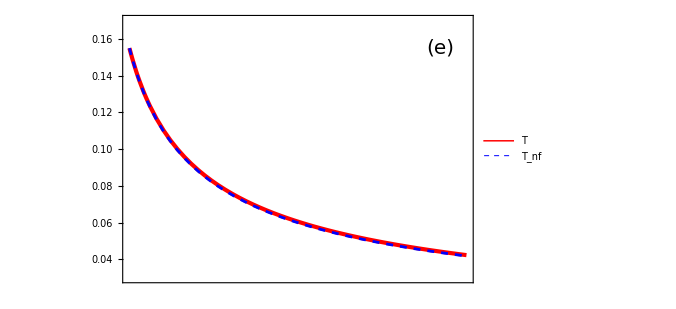

```mathematica
Plot[{TsolutionBoltzmannSpinFeedbackTransverse[τ]hbarc,TsolutionBoltzmannNoFeedbackTransverse[τ]hbarc},{τ,1.0,10.0},PlotRange->{{1,10},{0.03,0.17}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},
Axes->False,ImageSize->500,Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{{{0.04,"0.04",0.03},{0.035,"",0.01},{0.045,"",0.01},{0.05,"",0.015},{0.055,"",0.01},{0.06,"0.06",0.03},{0.065,"",0.01},{0.07,"",0.015},{0.075,"",0.01},{0.08,"0.08",0.03},{0.085,"",0.01},{0.09,"",0.015},{0.095,"",0.01},{0.10,"0.10",0.03},{0.105,"",0.01},{0.11,"",0.015},{0.115,"",0.01},{0.12,"0.12",0.03},{0.125,"",0.01},{0.13,"",0.015},{0.135,"",0.01},{0.14,"0.14",0.03},{0.145,"",0.01},{0.15,"",0.015},{0.155,"",0.01},{0.16,"0.16",0.03},{0.165,"",0.01}},None},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},None}},
Epilog->{Text[Style["(e)",FontSize->20],{9.3,0.155}],Rotate[Text[Style["T [GeV]",FontSize->19],{-0.3,0.1}],90Degree]},
PlotLegends->Placed[LineLegend[{"T","T_nf"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.85,0.35}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,10}}]
```

### PRC3f

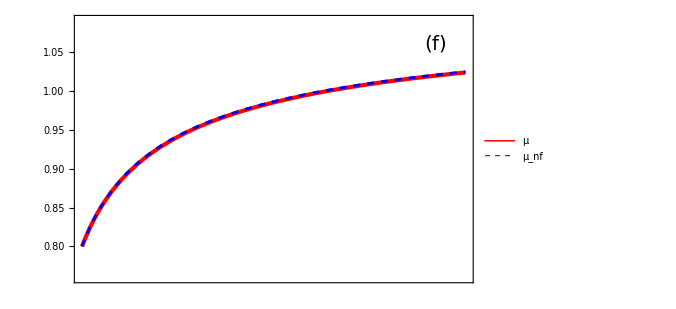

```mathematica
Plot[{μsolutionBoltzmannSpinFeedbackTransverse[τ]hbarc,μsolutionBoltzmannNoFeedbackTransverse[τ]hbarc},{τ,1.0,10.0},PlotRange->{{1,10},{0.76,1.09}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},Axes->False,ImageSize->500,
Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{None,{{0.77,"",0.015},{0.78,"",0.015},{0.79,"",0.015},{0.80,"0.80",0.03},{0.81,"",0.015},{0.82,"",0.015},{0.83,"",0.015},{0.84,"",0.015},{0.85,"0.85",0.03},{0.86,"",0.015},{0.87,"",0.015},{0.88,"",0.015},{0.89,"",0.015},{0.9,"0.90",0.03},{0.91,"",0.015},{0.92,"",0.015},{0.93,"",0.015},{0.94,"",0.015},{0.95,"0.95",0.03},{0.96,"",0.015},{0.97,"",0.015},{0.98,"",0.015},{0.99,"",0.015},{1,"1.00",0.03},{1.01,"",0.015},{1.02,"",0.015},{1.03,"",0.015},{1.04,"",0.015},{1.05,"1.05",0.03},{1.06,"",0.015},{1.07,"",0.015},{1.08,"",0.015},{1.10,"1.10",0.03}}},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},None}},
Epilog->{Text[Style["(f)",FontSize->20],{9.3,1.06}],Rotate[Text[Style["μ [GeV]",FontSize->19],{11.4,0.94}],-90Degree]},
PlotLegends->Placed[LineLegend[{"μ","μ_nf"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.15,0.8}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,10}}]
```

### PRC3g

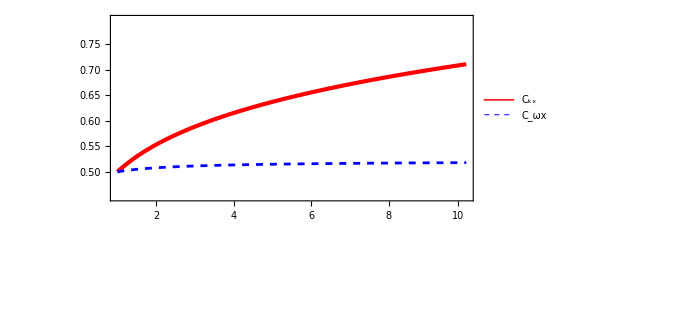

```mathematica
Plot[{CkxsolutionBoltzmannSpinFeedbackTransverse[τ],CwxsolutionBoltzmannSpinFeedbackTransverse[τ]} ,{τ,1.0,10.0},PlotRange->{{1,10},{0.45,0.8}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},Axes->False,ImageSize->500,
Frame->True,FrameStyle->Directive[Black, Thickness[0.008],14],

FrameTicks->{{{{0.5,"0.50",0.03},{0.55,"0.55", 0.03},{0.6,"0.60",0.03},{0.65,"0.65", 0.03},{0.7,"0.70",0.03},{0.75,"0.75", 0.03}},None},
{{{1.5,"",0.015},{2.,"2",0.03},{2.5,"",0.015},{3.,"3",0.03},{3.5,"",0.015},{4.,"4",0.03},{4.5,"",0.015},{5.,"5",0.03},{5.5,"",0.015},{6.,"6",0.03},{6.5,"",0.015},{7.,"7",0.03},{7.5,"",0.015},{8.,"8",0.03},{8.5,"",0.015},{9.,"9",0.03},{9.5,"",0.015},{9.8,"10",0}},{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015},10}}},
Epilog->{Text[Style["(g)",FontSize->20],{9.3,4.5}],Text[Style["τ [fm]",FontSize->19],{5.5,-0.15}],Rotate[Text[Style["C_k, C_ω",FontSize->19],{-0.1,0.625}],90Degree]},
PlotLegends->Placed[LineLegend[{"C_kx","C_ωx"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.15,0.7}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,5}}]
```

### PRC3h

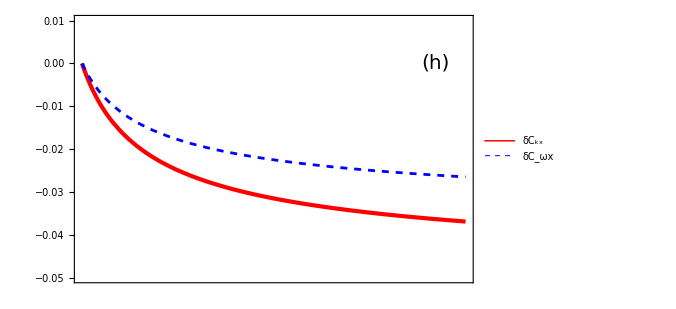

```mathematica
Plot[{CkxsolutionBoltzmannSpinFeedbackTransverse[τ]/CkxsolutionBoltzmannNoFeedbackTransverse[τ]-1,CwxsolutionBoltzmannSpinFeedbackTransverse[τ]/CwxsolutionBoltzmannNoFeedbackTransverse[τ]-1},{τ,1.0,10.0},PlotRange->{{1,10},{-0.05,0.01}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},Axes->False,ImageSize->500,
Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{None,{{-0.04,"-0.04",0.03},{-0.03,"",0.015},{-0.02,"-0.02",0.03},{-0.01,"",0.015},{0,"0",0.03}}},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},None}},
Epilog->{Text[Style["(h)",FontSize->20],{9.3,0}],Rotate[Text[Style["δC_k,δC_ω",FontSize->19],{11.4,-0.02}],-90Degree]},
PlotLegends->Placed[LineLegend[{"δC_kx","δC_ωx"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.7,0.7}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,10}}]
```

### Fermi 3e

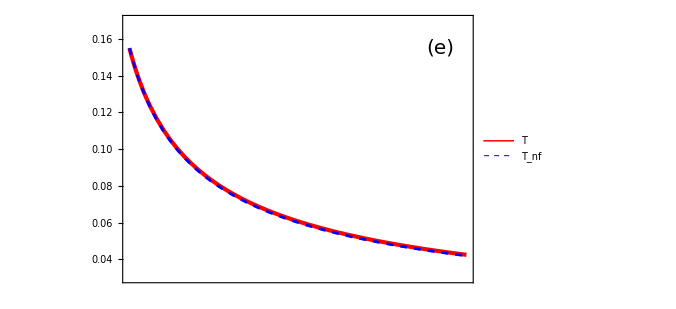

```mathematica
Plot[{TsolutionFermiSpinFeedbackTransverse[τ]hbarc,TsolutionFermiNoFeedbackTransverse[τ]hbarc},{τ,1.0,10.0},PlotRange->{{1,10},{0.03,0.17}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},
Axes->False,ImageSize->500,Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{{{0.04,"0.04",0.03},{0.035,"",0.01},{0.045,"",0.01},{0.05,"",0.015},{0.055,"",0.01},{0.06,"0.06",0.03},{0.065,"",0.01},{0.07,"",0.015},{0.075,"",0.01},{0.08,"0.08",0.03},{0.085,"",0.01},{0.09,"",0.015},{0.095,"",0.01},{0.10,"0.10",0.03},{0.105,"",0.01},{0.11,"",0.015},{0.115,"",0.01},{0.12,"0.12",0.03},{0.125,"",0.01},{0.13,"",0.015},{0.135,"",0.01},{0.14,"0.14",0.03},{0.145,"",0.01},{0.15,"",0.015},{0.155,"",0.01},{0.16,"0.16",0.03},{0.165,"",0.01}},None},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},None}},
Epilog->{Text[Style["(e)",FontSize->20],{9.3,0.155}],Rotate[Text[Style["T [GeV]",FontSize->19],{-0.3,0.1}],90Degree]},
PlotLegends->Placed[LineLegend[{"T","T_nf"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.85,0.35}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,10}}]
```

### Fermi 3f

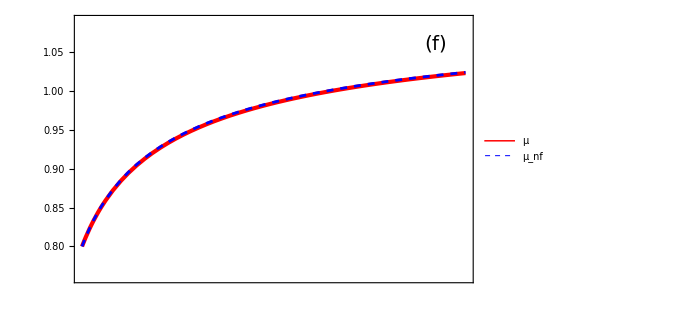

```mathematica
Plot[{μsolutionFermiSpinFeedbackTransverse[τ]hbarc,μsolutionFermiNoFeedbackTransverse[τ]hbarc},{τ,1.0,10.0},PlotRange->{{1,10},{0.76,1.09}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},Axes->False,ImageSize->500,
Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{None,{{0.77,"",0.015},{0.78,"",0.015},{0.79,"",0.015},{0.80,"0.80",0.03},{0.81,"",0.015},{0.82,"",0.015},{0.83,"",0.015},{0.84,"",0.015},{0.85,"0.85",0.03},{0.86,"",0.015},{0.87,"",0.015},{0.88,"",0.015},{0.89,"",0.015},{0.9,"0.90",0.03},{0.91,"",0.015},{0.92,"",0.015},{0.93,"",0.015},{0.94,"",0.015},{0.95,"0.95",0.03},{0.96,"",0.015},{0.97,"",0.015},{0.98,"",0.015},{0.99,"",0.015},{1,"1.00",0.03},{1.01,"",0.015},{1.02,"",0.015},{1.03,"",0.015},{1.04,"",0.015},{1.05,"1.05",0.03},{1.06,"",0.015},{1.07,"",0.015},{1.08,"",0.015},{1.10,"1.10",0.03}}},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},None}},
Epilog->{Text[Style["(f)",FontSize->20],{9.3,1.06}],Rotate[Text[Style["μ [GeV]",FontSize->19],{11.4,0.94}],-90Degree]},
PlotLegends->Placed[LineLegend[{"μ","μ_nf"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.15,0.8}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,10}}]
```

### Fermi 3g

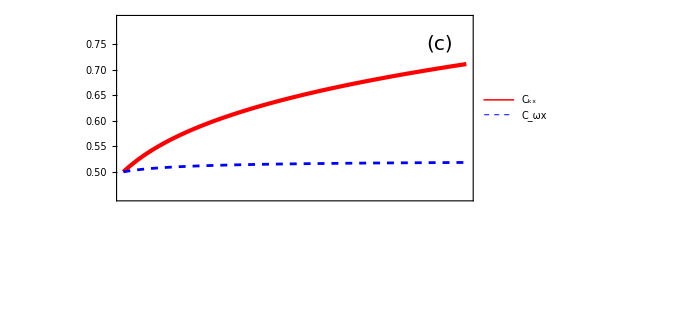

```mathematica
Plot[{CkxsolutionFermiSpinFeedbackTransverse[τ],CwxsolutionFermiSpinFeedbackTransverse[τ]} ,{τ,1.0,10.0},PlotRange->{{1,10},{0.45,0.8}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},Axes->False,ImageSize->500,
Frame->True,FrameStyle->Directive[Black, Thickness[0.008],14],

FrameTicks->{{{{0.5,"0.50",0.03},{0.55,"0.55", 0.03},{0.6,"0.60",0.03},{0.65,"0.65", 0.03},{0.7,"0.70",0.03},{0.75,"0.75", 0.03}},None},
{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015},{9.8,"",0}},{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}}}},
Epilog->{Text[Style["(c)",FontSize->20],{9.3,0.75}],Text[Style["τ [fm]",FontSize->19],{5.5,-0.15}],Rotate[Text[Style["C_k, C_ω",FontSize->19],{-0.2,0.625}],90Degree]},
PlotLegends->Placed[LineLegend[{"C_kx","C_ωx"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.2,0.8}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,5}}]
```

### Fermi 3h

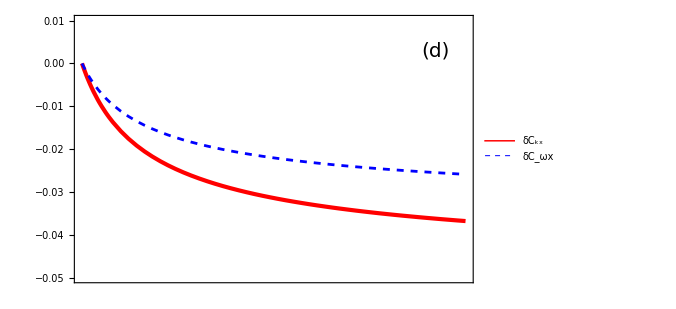

```mathematica
Plot[{CkxsolutionFermiSpinFeedbackTransverse[τ]/CkxsolutionFermiNoFeedbackTransverse[τ]-1,CwxsolutionFermiSpinFeedbackTransverse[τ]/CwxsolutionFermiNoFeedbackTransverse[τ]-1},{τ,1.0,10.0},PlotRange->{{1,10},{-0.05,0.01}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},Axes->False,ImageSize->500,
Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{None,{{-0.04,"-0.04",0.03},{-0.03,"",0.015},{-0.02,"-0.02",0.03},{-0.01,"",0.015},{0,"0",0.03}}},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015},{9.8,"",0}},{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}}}},
Epilog->{Text[Style["(d)",FontSize->20],{9.3,0.003}],Rotate[Text[Style["δC_k,δC_ω",FontSize->19],{11.4,-0.02}],-90Degree]},
PlotLegends->Placed[LineLegend[{"δC_kx","δC_ωx"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.5,0.8}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,10}}]
```

### Fermi 3n

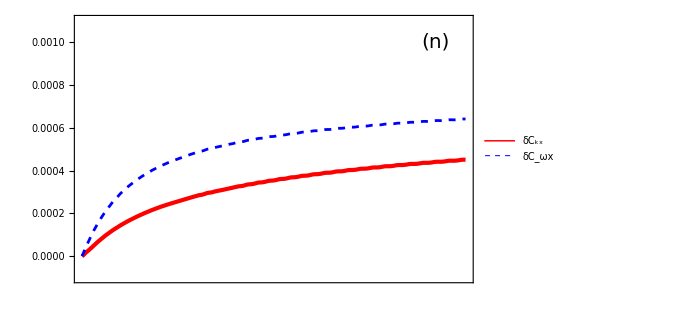

```mathematica
Plot[{CkxsolutionFermiSpinFeedbackTransverse[τ]/CkxsolutionBoltzmannSpinFeedbackTransverse[τ]-1,CwxsolutionFermiSpinFeedbackTransverse[τ]/CwxsolutionBoltzmannSpinFeedbackTransverse[τ]-1},{τ,1.0,10.0},PlotRange->{{1,10},{-0.0001,0.0011}},
PlotStyle->{Directive[Red,Thickness[0.006]],Directive[Blue,Thickness[0.004],Dashed]},Axes->False,ImageSize->500,
Frame->True,FrameStyle->Directive[Black,Thickness[0.008],14],
FrameTicks->{{None,{{0,"0",0.03},{0.0001,"",0.015},{0.0002,"",0.015},{0.0003,"",0.015},{0.0004,"",0.015},{0.0005,"0.0005",0.03},{0.0006,"",0.015},{0.0007,"",0.015},{0.0008,"",0.015},{0.0009,"",0.015},{0.001,"0.001",0.03}}},{{{1.5,"",0.015},{2.,"",0.03},{2.5,"",0.015},{3.,"",0.03},{3.5,"",0.015},{4.,"",0.03},{4.5,"",0.015},{5.,"",0.03},{5.5,"",0.015},{6.,"",0.03},{6.5,"",0.015},{7.,"",0.03},{7.5,"",0.015},{8.,"",0.03},{8.5,"",0.015},{9.,"",0.03},{9.5,"",0.015}},None}},
Epilog->{Text[Style["(n)",FontSize->20],{9.3,0.001}],Rotate[Text[Style["δC_k,δC_ω",FontSize->19],{11.6,0.0005}],-90Degree]},
PlotLegends->Placed[LineLegend[{"δC_kx","δC_ωx"},LabelStyle->{FontSize->14,Darker[Black,0.1],Plain}],Scaled[{0.15,0.75}]],PlotRangeClipping->False,ImagePadding->{{80,70},{70,10}}]
```